Computational Physics Laboratory
- Tree-Level Gluon Scattering

```mathematica
(*Lanciamo un numero di kernel corrispondenti al numero di core del computer, utile per eseguire calcolo parallelo di espressioni*)
CloseKernels[];
LaunchKernels[$ProcessorCount];
```

```mathematica
(*---Formattazioni dell'output---*)
Format[mu[i_]] := Subscript[μ, i]; (*indici di Lorentz*)
Format[nu[i_]] := Subscript[ν, i];
Format[s[i_, j_]] := Subscript[s, i, j]; (*variabili di Mandelstam generalizzate*)
Format[p[a_]] := Subscript[p, a]; (*impulso*)
Format[e[a_]] := Subscript[ϵ, a]; (*vettore di polarizzazione*)
Format[c[a_]] := Subscript[c, a]; (*carica di colore*)
Format[SP[v_,{mu_[i_]}]]:=Superscript[v,mu[i]]; (*quadrivettori*)
Format[SP[expr_+p___,{mu_[i_]}]]:=Superscript[Row[{"(",expr + p,")"}],mu[i]]; (*quadrivettore somma*)
(*Format[SP[n,{mu_[i_]}]]:=Superscript[n,mu[i]];*)
Format[SP[a_, b_]] := a* b; (*prodotti scalari*)
Format[SP[{mu[a_]}, {mu[b_]}]]:=Subscript[g, mu[a], mu[b]]; (*metrica*)
Format[SP[{nu[a_]}, {nu[b_]}]]:=Subscript[g, nu[a], nu[b]];
Format[SP[{mu[a_]}, {nu[b_]}]]:=Subscript[g, mu[a], nu[b]];
Format[delta[f_[a_], g_[b_]]] := Subscript[δ, f [a], g[b]]; (*delta*)
Format[f[f1_[a_], f2_[b_], f3_[c_]]] := Subscript[f,f1[a], f2[b], f3[c]]; (*costanti di struttura*)
Format[T[i_]] := Superscript[T, i]; (*generatori dell'algebra*)
Format[T[i_][ j_, k_]] := Subscript[T[i], j, k]; (*in componenti*)

SetAttributes[SP, Orderless]; (*in che ordine sono messi gli indici non ha importanza*)
SetAttributes[delta, Orderless];
SetAttributes[s, Orderless];

h = -4; (*variabile globale per enumerare gli indici sommati*)
```

## Diagrams generations

### Graphs generation

```mathematica
grafobase={{1,-1},{2,-1},{3,-1}}; (*grafo iniziale*)

(*Aggiunge un vertice a 3 sostituendo una linea con tre nuove*)
inserisci3[pos_,ext_,int_,grafo_]:=Module[{temp,pippo,pos1,pos2},pos1=grafo[[pos,1]];
pos2=grafo[[pos,2]];
temp=ReplacePart[grafo,pippo[{ext,int},{pos1,int},{pos2,int}],pos];
temp/. {pippo->Sequence}];

(*Applica inserisci3 a tutte le linee del grafo*)
inserzione3[grafo_]:=Module[{nuovigrafi,indici,npt,nvert},indici=Flatten[grafo];
npt=Max[indici];
nvert=Min[indici];
nuovigrafi=Table[inserisci3[i,npt+1,nvert-1,grafo],{i,1,Length[grafo]}];
Return[nuovigrafi]];

(*Aggiunge un punto esterno a un vertice a 3*)
inserisci4[vertice_,ext_,grafo_]:=If[Count[grafo,vertice,Infinity]===3,Append[grafo,{ext,vertice}],{}];

(*Applica inserisci4 a tutti i vertici del grafo*)
inserzione4[grafo_]:=Module[{nuovigrafi,npt,nvert,indici},indici=Flatten[grafo];
npt=Max[indici];
nvert=Min[indici];
nuovigrafi=Table[inserisci4[i,npt+1,grafo],{i,-1,nvert,-1}];
Return[nuovigrafi]];

(*Costruisce iterativamente tutti i grafi fino a n punti esterni*)
generagrafi[n_,grafo_]:=Module[{temp,listagrafi,nuovigrafi3,nuovigrafi4,indici},indici=Flatten[grafo];
j=Max[indici];
listagrafi={grafo};
While[j<n,nuovigrafi3=Flatten[Map[inserzione3,listagrafi],1];
nuovigrafi4=Flatten[Map[inserzione4,listagrafi],1];
listagrafi=DeleteCases[Join[nuovigrafi3,nuovigrafi4],{}];
j=j+1;];
Return[listagrafi]];

(*---Generazione di tutti i grafi possibili con 4 e 5 linee esterne---*)
generagrafi[4, grafobase]
generagrafi[5, grafobase]
```

{{{4,-2},{1,-2},{-1,-2},{2,-1},{3,-1}},{{1,-1},{4,-2},{2,-2},{-1,-2},{3,-1}},{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2}},{{1,-1},{2,-1},{3,-1},{4,-1}}}

{{{5,-3},{4,-3},{-2,-3},{1,-2},{-1,-2},{2,-1},{3,-1}},{{4,-2},{5,-3},{1,-3},{-2,-3},{-1,-2},{2,-1},{3,-1}},{{4,-2},{1,-2},{5,-3},{-1,-3},{-2,-3},{2,-1},{3,-1}},{{4,-2},{1,-2},{-1,-2},{5,-3},{2,-3},{-1,-3},{3,-1}},{{4,-2},{1,-2},{-1,-2},{2,-1},{5,-3},{3,-3},{-1,-3}},{{5,-3},{1,-3},{-1,-3},{4,-2},{2,-2},{-1,-2},{3,-1}},{{1,-1},{5,-3},{4,-3},{-2,-3},{2,-2},{-1,-2},{3,-1}},{{1,-1},{4,-2},{5,-3},{2,-3},{-2,-3},{-1,-2},{3,-1}},{{1,-1},{4,-2},{2,-2},{5,-3},{-1,-3},{-2,-3},{3,-1}},{{1,-1},{4,-2},{2,-2},{-1,-2},{5,-3},{3,-3},{-1,-3}},{{5,-3},{1,-3},{-1,-3},{2,-1},{4,-2},{3,-2},{-1,-2}},{{1,-1},{5,-3},{2,-3},{-1,-3},{4,-2},{3,-2},{-1,-2}},{{1,-1},{2,-1},{5,-3},{4,-3},{-2,-3},{3,-2},{-1,-2}},{{1,-1},{2,-1},{4,-2},{5,-3},{3,-3},{-2,-3},{-1,-2}},{{1,-1},{2,-1},{4,-2},{3,-2},{5,-3},{-1,-3},{-2,-3}},{{5,-2},{1,-2},{-1,-2},{2,-1},{3,-1},{4,-1}},{{1,-1},{5,-2},{2,-2},{-1,-2},{3,-1},{4,-1}},{{1,-1},{2,-1},{5,-2},{3,-2},{-1,-2},{4,-1}},{{1,-1},{2,-1},{3,-1},{5,-2},{4,-2},{-1,-2}},{{4,-2},{1,-2},{-1,-2},{2,-1},{3,-1},{5,-1}},{{4,-2},{1,-2},{-1,-2},{2,-1},{3,-1},{5,-2}},{{1,-1},{4,-2},{2,-2},{-1,-2},{3,-1},{5,-1}},{{1,-1},{4,-2},{2,-2},{-1,-2},{3,-1},{5,-2}},{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2},{5,-1}},{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2},{5,-2}}}

Punti esterni | Numero grafi
4 | 4
5 | 25
6 | 220
7 | 2485
8 | 34300
9 | 559405

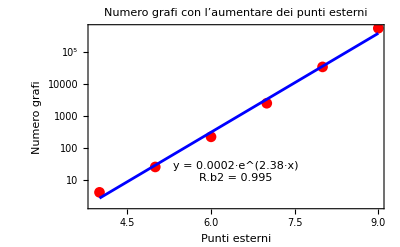

R.b2 = 0.994747

```mathematica
(*Calcolo del numero di grafi per ciascun numero di punti esterni*)next=Range[4,9];
ngrafi=Table[Length[generagrafi[i,grafobase]],{i,next}];

(*Tabella riassuntiva*)
Grid[Prepend[Transpose[{next,ngrafi}],{"Punti esterni","Numero grafi"}],Frame->All,Background->{None,{{LightGray}}},Alignment->Left]

(*Preparo i dati per il fit*)
data=Transpose[{next,ngrafi}];
xVals=next;
yVals=ngrafi;
logYVals=Log[yVals];

(*Fit lineare:log(y)=log(a)+b x=>y=a Exp[b x]*)
logFit=LinearModelFit[Transpose[{xVals,logYVals}],x,x];

(*Ricavo i parametri esponenziali*)
bFitted=logFit["BestFitParameters"][[2]];
aFitted=Exp[logFit["BestFitParameters"][[1]]];

(*Plot con funzione di fit e R^2*)
Show[ListPlot[data,PlotStyle->{Red,PointSize[Medium]},PlotMarkers->Automatic,Frame->True,FrameLabel->{"Punti esterni","Numero grafi"},GridLines->Automatic,ScalingFunctions->{"Linear","Log"},PlotRange->All],Plot[aFitted Exp[bFitted x],{x,Min[xVals],Max[xVals]},PlotStyle->Blue,ScalingFunctions->{"Linear","Log"}],Epilog->{Inset[Column[{Style["y = "<>ToString[NumberForm[aFitted,{10,4}]]<>"·e^("<>ToString[NumberForm[bFitted,{3,2}]]<>"·x)",Medium,Black],Style["R.b2 = "<>ToString[NumberForm[logFit["RSquared"],{3,3}]],Medium,Black]}],Scaled[{0.5,0.2}]]},PlotLabel->Style["Numero grafi con l’aumentare dei punti esterni",Small,Bold]]

(*Stampa R^2 separatamente,opzionale*)
Print["R.b2 = ",logFit["RSquared"]];

(*Pulizia finale*)
Clear[next,ngrafi,data,aFitted,bFitted,logFit];
```

### Field theory implementation

```mathematica
(*Restituisce la lista degli impulsi associati alle linee del grafo*)listaimpulsi[grafo_]:=Map[Apply[p,#]&,grafo]

(*Sostituisce {i,j} con p[i,j] nel primo elemento di ogni coppia*)
applicaimpulsi[grafo_]:=MapAt[Apply[p,#]&,grafo,{All,1}]

(*Genera le equazioni di conservazione del momento per ogni vertice*)
generaequazioni[grafo_]:=Module[{temp},indici=Flatten[grafo];
npt=Max[indici];(*numero di punti esterni*)nvert=Min[indici];(*numero di vertici*)impulsi=listaimpulsi[grafo];
(*Conservazione del momento per ciascun vertice*)equazioni=Table[impulsivertice=Join[Cases[impulsi,p[_,i]],-Cases[impulsi,p[i,_]]];
eq=Apply[Plus,impulsivertice]==0,{i,-1,nvert,-1}];
(*Rinomina p[i,j]->p[i] se i>0*)equazioni=equazioni/. p[i_/;i>0,j_]:>p[i];
(*Impulsi interni=p[i,j] non rinominati*)incognite=Cases[equazioni,p[_,_],Infinity];
(*Conservazione globale:p_n=-Σp_i*)globale=Rule[p[npt],-Sum[p[k],{k,1,npt-1}]];
equazioni=equazioni/. globale;
impulsiinterni=Solve[equazioni,incognite];
Return[impulsiinterni]];

(*Aggiunge indici di Lorentz e colore a ciascuna linea*)
addIndices[grafo_]:=Module[{newgrafo},newgrafo=Table[{grafo[[i]],mu[grafo[[i,1]]],c[grafo[[i,1]]],If[grafo[[i,1]]<0,Sequence@@{mu[grafo[[i,2]]],c[grafo[[i,2]]]},Nothing]},{i,1,Length[grafo]}]];

(*Costruisce l'espressione associata a un grafo*)
diagramma[grafo_]:=Module[{numeriinterni,newgrafo},newgrafo=addIndices[grafo];
regole=generaequazioni[grafo];
(*Linee interne del grafo*)interne=Cases[newgrafo,{{i_/;i<0,j_/;j<0},___}];
numeriinterni=applicaimpulsi[interne]/. regole[[1]];
propagatori=Apply[Times,Map[Prop,numeriinterni]];
(*Vertici:calcolo momento+indici per ciascun vertice*)vertici=Table[linee=applicaimpulsi[newgrafo];
lineevertice=Join[Cases[linee,{p[a_,i],rest___}:>{p[a,i],rest}],Cases[linee,{p[i,b_],rest___}:>{-p[i,b],rest}]];
lineevertice=lineevertice/. regole[[1]];
lineevertice=lineevertice/. {p[i_/;i>0,j_],rest___}:>{p[i],rest};
lineevertice=lineevertice/. {momentum___,mu[j_],c[j_],mu[k_],c[k_]}:>If[j===i,{momentum,mu[If[k>0,k,{k,i}]],c[If[k>0,k,{k,i}]]},{momentum,mu[{j,i}],c[{j,i}]}];
vertice=If[Length[lineevertice]===3,V3[i][lineevertice],V4[i][lineevertice]];
vertice,{i,-1,nvert,-1}];
vertici=Apply[Times,vertici];
Return[propagatori*vertici]];

(*Genera tutti i diagrammi con n linee esterne*)
generadiagrammi[n_,grafo_]:=Module[{temp},grafi=generagrafi[n,grafo];
diagrammi=Map[diagramma,grafi];
Return[diagrammi]];

(*Esegui:aggiunta indici+generazione diagrammi*)
addIndices/@generagrafi[4,grafobase]
generadiagrammi[4,grafobase]

(*Nota:se una linea collega due punti interni,il suo indice è {interno,vertice}.Questo aiuta a distinguere contrazioni interne vs esterne nel calcolo simbolico.*)
```

{{{{4,-2},μ_4,c_4},{{1,-2},μ_1,c_1},{{-1,-2},μ_-1,c_-1,μ_-2,c_-2},{{2,-1},μ_2,c_2},{{3,-1},μ_3,c_3}},{{{1,-1},μ_1,c_1},{{4,-2},μ_4,c_4},{{2,-2},μ_2,c_2},{{-1,-2},μ_-1,c_-1,μ_-2,c_-2},{{3,-1},μ_3,c_3}},{{{1,-1},μ_1,c_1},{{2,-1},μ_2,c_2},{{4,-2},μ_4,c_4},{{3,-2},μ_3,c_3},{{-1,-2},μ_-1,c_-1,μ_-2,c_-2}},{{{1,-1},μ_1,c_1},{{2,-1},μ_2,c_2},{{3,-1},μ_3,c_3},{{4,-1},μ_4,c_4}}}

{Prop[{p_2+p_3,μ_-1,c_-1,μ_-2,c_-2}] V3[-2][{{p_4,μ_4,c_4},{p_1,μ_1,c_1},{p_2+p_3,μ_{-1,-2},c_{-1,-2}}}] V3[-1][{{p_2,μ_2,c_2},{p_3,μ_3,c_3},{-p_2-p_3,μ_{-2,-1},c_{-2,-1}}}],Prop[{p_1+p_3,μ_-1,c_-1,μ_-2,c_-2}] V3[-2][{{p_4,μ_4,c_4},{p_2,μ_2,c_2},{p_1+p_3,μ_{-1,-2},c_{-1,-2}}}] V3[-1][{{p_1,μ_1,c_1},{p_3,μ_3,c_3},{-p_1-p_3,μ_{-2,-1},c_{-2,-1}}}],Prop[{p_1+p_2,μ_-1,c_-1,μ_-2,c_-2}] V3[-2][{{p_4,μ_4,c_4},{p_3,μ_3,c_3},{p_1+p_2,μ_{-1,-2},c_{-1,-2}}}] V3[-1][{{p_1,μ_1,c_1},{p_2,μ_2,c_2},{-p_1-p_2,μ_{-2,-1},c_{-2,-1}}}],V4[-1][{{p_1,μ_1,c_1},{p_2,μ_2,c_2},{p_3,μ_3,c_3},{p_4,μ_4,c_4}}]}

```mathematica
(*---Regole di Feynman---*)
FeynRules = # //. {

(*propagatore gluonico:*)
Prop[{p1_, mu1_, c1_, mu2_, c2_}] :> - I (delta[c1, c2]SP[{mu1}, {mu2}])/SP[p1, p1]  ,

(*vertice a tre gluoni:*)
V3[i_][{{p1_, mu1_, c1_}, {p2_, mu2_, c2_}, {p3_, mu3_, c3_}}] :> - g f[c1, c2, c3]*(SP[{mu1}, {mu2}]SP[p1 - p2, {mu3}] + SP[{mu2}, {mu3}]SP[p2 - p3, {mu1}] + SP[{mu3}, {mu1}]SP[p3 - p1, {mu2}]),

(*vertice a quattro gluoni:*)
V4[i_][{{p1_, mu1_, c1_}, {p2_, mu2_, c2_}, {p3_, mu3_, c3_}, {p4_, mu4_, c4_}}] :> - I  g^2 (f[c1, c2, c[i]] f[c3, c4, c[i]](SP[{mu1}, {mu3}]SP[{mu2}, {mu4}] - SP[{mu1}, {mu4}]SP[{mu2}, {mu3}]) + f[c1, c3, c[i]] f[c2, c4, c[i]](SP[{mu1}, {mu2}]SP[{mu3}, {mu4}] - SP[{mu1}, {mu4}]SP[{mu2}, {mu3}]) + f[c1, c4, c[i]] f[c2, c3, c[i]](SP[{mu1}, {mu2}]SP[{mu3}, {mu4}] - SP[{mu1}, {mu3}]SP[{mu2}, {mu4}]))
(*chiamiamo in maniera generica l'indice sommato*)
} &;

(*---Applichiamo le regole di Feynman a ciascun diagramma con quattro linee esterne, così da ottenere le rispettive ampiezze---*)
M4  = generadiagrammi[4, grafobase] // FeynRules;

schannel = M4[[3]];
tchannel = M4[[2]];
uchannel = M4[[1]];
fourvertex = M4[[4]];

Print[Row[{Subscript[ℳ,"s"]," = ",schannel}]]
Print[Row[{Subscript[ℳ,"t"]," = ",tchannel}]]
Print[Row[{Subscript[ℳ,"u"]," = ",uchannel}]]
Print[Row[{Subscript[ℳ,"4"]," = ",fourvertex}]]
```

ℳ_s = -1/(p_1+p_2)^2ⅈ g^2 δ_(c_-2,c_-1) f_(c_1,c_2,c_{-2,-1}) f_(c_4,c_3,c_{-1,-2}) g_(μ_-2,μ_-1) ((p_1+2 p_2)^μ_1 g_(μ_2,μ_{-2,-1})+g_(μ_1,μ_{-2,-1}) (-2 p_1-p_2)^μ_2+g_(μ_1,μ_2) (p_1-p_2)^(μ_{-2,-1})) ((p_1+p_2-p_4)^μ_3 g_(μ_4,μ_{-1,-2})+g_(μ_3,μ_{-1,-2}) (-p_1-p_2+p_3)^μ_4+g_(μ_3,μ_4) (-p_3+p_4)^(μ_{-1,-2}))

ℳ_t = -1/(p_1+p_3)^2ⅈ g^2 δ_(c_-2,c_-1) f_(c_1,c_3,c_{-2,-1}) f_(c_4,c_2,c_{-1,-2}) g_(μ_-2,μ_-1) ((p_1+2 p_3)^μ_1 g_(μ_3,μ_{-2,-1})+g_(μ_1,μ_{-2,-1}) (-2 p_1-p_3)^μ_3+g_(μ_1,μ_3) (p_1-p_3)^(μ_{-2,-1})) ((p_1+p_3-p_4)^μ_2 g_(μ_4,μ_{-1,-2})+g_(μ_2,μ_{-1,-2}) (-p_1+p_2-p_3)^μ_4+g_(μ_2,μ_4) (-p_2+p_4)^(μ_{-1,-2}))

ℳ_u = -1/(p_2+p_3)^2ⅈ g^2 δ_(c_-2,c_-1) f_(c_2,c_3,c_{-2,-1}) f_(c_4,c_1,c_{-1,-2}) g_(μ_-2,μ_-1) ((p_2+2 p_3)^μ_2 g_(μ_3,μ_{-2,-1})+g_(μ_2,μ_{-2,-1}) (-2 p_2-p_3)^μ_3+g_(μ_2,μ_3) (p_2-p_3)^(μ_{-2,-1})) ((p_2+p_3-p_4)^μ_1 g_(μ_4,μ_{-1,-2})+g_(μ_1,μ_{-1,-2}) (p_1-p_2-p_3)^μ_4+g_(μ_1,μ_4) (-p_1+p_4)^(μ_{-1,-2}))

ℳ_4 = -ⅈ g^2 (f_(c_1,c_2,c_-1) f_(c_3,c_4,c_-1) (-g_(μ_1,μ_4) g_(μ_2,μ_3)+g_(μ_1,μ_3) g_(μ_2,μ_4))+f_(c_1,c_3,c_-1) f_(c_2,c_4,c_-1) (-g_(μ_1,μ_4) g_(μ_2,μ_3)+g_(μ_1,μ_2) g_(μ_3,μ_4))+f_(c_1,c_4,c_-1) f_(c_2,c_3,c_-1) (-g_(μ_1,μ_3) g_(μ_2,μ_4)+g_(μ_1,μ_2) g_(μ_3,μ_4)))

```mathematica
(*---Definiamo delle regole per effettuare prodotti scalari tra strutture di colore e di Lorentz---*)

(*---Prodotti psedoscalari---*)
LorentzSP = #  //. {
SP[a_, {mu_}] SP[b_, {mu_}] :> SP[a, b],
SP[a_, {mu_}] SP[a_, {mu_}] :> SP[a, a],
SP[{mu_}, {mu_}] :> 4, (*traccia della metrica*)
SP[n, n] :> 0, (*gauge condition*)
SP[p[a_], p[a_]] :> 0, (*i gluoni sono particelle massless*)
SP[p[a_], e[a_]] :> 0  (*polarizzazioni trasverse*)
} &;

(*---Prodotti pseudoscalari tra punti interni---*)
LorentzSPinternal = # //. {
SP[{mu[i_]}, {mu[j_]}] SP[a_, {mu[{i_, j_}]}] SP[b_, {mu[{j_, i_}]}]  :> SP[a, b],
SP[{mu[i_]}, {mu[j_]}]SP[{mu[{i_, j_}]}, a_] :> SP[mu[j], a],
SP[p[a_], p[a_]] :> 0 (*i gluoni sono particelle massless*)
} &;

(*---Linearità e omogeneità delle strutture di Lorentz---*)
ExpandLorentz = # //. {
SP[c_?NumericQ*a_,b_]:>c SP[a,b],
SP[a_ + b_, c_] :> SP[a, c] + SP[b, c]
} &;

(*---Operazioni tra fattori di colore---*)
colourSP  = # //.{
(*delta applicata agli indici interni*)
delta[c[a_],c[b_]] f[args1___] f[args2___] /; MemberQ[{args1},c[{a,b}]] && MemberQ[{args2},c[{b,a}]] && b < a :>Module[{replaced},
replaced=f @@ ReplacePart[{args1},FirstPosition[{args1},c[{a,b}]]:>c[h-1]] f @@ ReplacePart[{args2},FirstPosition[{args2},c[{b,a}]]:>c[h = h-1]] ],
(*delta applicata a tutti gli altri casi*)
delta[i_,j_]*rest_:>(rest/. i->j),
(*prodotto tra due delta*)
delta[a_, b_] delta[a_, c_] :> delta[b, c]
} &;
```

```mathematica
(*Analisi dei costi simbolici:per le prime ampiezze con n = 4, 5 e 6,misuriamo memoria occupata e tempo di esecuzione nei tre passaggi chiave: espansione, contrazione degli indici interni, semplificazione.*)

M5=ParallelMap[FeynRules, generadiagrammi[5,grafobase]];
M6=ParallelMap[FeynRules,generadiagrammi[6,grafobase]];
M7=ParallelMap[FeynRules,generadiagrammi[7,grafobase]];

firstamps = {M4[[1]], M5[[1]], M6[[1]], M7[[1]]};

Do[
Print["=== Symbolic processing stages for the first n =",  i+3, " amplitude ==="];
startsize=ByteCount[firstamps[[i]]];
ti=AbsoluteTime[];
appo=firstamps[[i]]//ExpandLorentz//Expand;
tf=AbsoluteTime[];
finalsize=ByteCount[appo];
Print["Time taken to Expand: ",tf-ti," s"];
Print["Initial and final memory usage: ",startsize," B → ",finalsize," B"];
(*startsize=finalsize;
ti=AbsoluteTime[];
appo=appo//colourSP;
tf=AbsoluteTime[];
finalsize=ByteCount[appo];
Print["Time taken to colourSP: ",tf-ti," s"];
Print["Initial and final memory usage: ",startsize," B → ",finalsize," B"];*)
startsize=finalsize;
ti=AbsoluteTime[];
appo=appo//LorentzSPinternal;
tf=AbsoluteTime[];
finalsize=ByteCount[appo];
Print["Time taken to contract internal indices: ",tf-ti," s"];
Print["Initial and final memory usage: ",startsize," B → ",finalsize," B"];
startsize=finalsize;
ti=AbsoluteTime[];
appo=appo//Simplify;
tf=AbsoluteTime[];
finalsize=ByteCount[appo];
Print["Time taken to simplify the expression: ",tf-ti," s"];
Print["Initial and final memory usage: ",startsize," B → ",finalsize," B"]
, {i, 1, Length[firstamps]}]

Clear[appo, startsize,finalsize,tf,ti]
```

=== Symbolic processing stages for the first n =4 amplitude ===

Time taken to Expand: 0. s

Initial and final memory usage: 7264 B → 159024 B

Time taken to contract internal indices: 0.0075658 s

Initial and final memory usage: 159024 B → 88704 B

Time taken to simplify the expression: 0.167808 s

Initial and final memory usage: 88704 B → 34192 B

=== Symbolic processing stages for the first n =5 amplitude ===

Time taken to Expand: 0.033956 s

Initial and final memory usage: 12240 B → 3410208 B

Time taken to contract internal indices: 0.172046 s

Initial and final memory usage: 3410208 B → 1180472 B

Time taken to simplify the expression: 0.8175611 s

Initial and final memory usage: 1180472 B → 327664 B

=== Symbolic processing stages for the first n =6 amplitude ===

Time taken to Expand: 0.346424 s

Initial and final memory usage: 17920 B → 80809472 B

Time taken to contract internal indices: 5.2625516 s

Initial and final memory usage: 80809472 B → 17225696 B

Time taken to simplify the expression: 41.9192568 s

Initial and final memory usage: 17225696 B → 3490568 B

=== Symbolic processing stages for the first n =7 amplitude ===

Time taken to Expand: 9.321112 s

Initial and final memory usage: 24072 B → 2126987600 B

Time taken to contract internal indices: 217.800911 s

Initial and final memory usage: 2126987600 B → 272610664 B

Time taken to simplify the expression: 1146.327188 s

Initial and final memory usage: 272610664 B → 42329456 B

## Ward identity

```mathematica
(*---Regole utili per la verifica dell'identità di Ward---*)

(*---Sostituzione che permuta gli indici di una costante di struttura in maniera ordinata--*)
Perm := {
f[c[i_], c[j_], c[k_]] :> Signature[{i, j, k}]*f[Sequence @@ Map[c, Sort[{i, j, k}]]]
};

(*---Cambia il nome agli indici sommati---*)
summedIndices = # /. Perm //. {
f[c[i_], c[a_], c[b_]] f[c[i_], c[d_], c[e_]] /; AllTrue[{a, b, d, e}, Positive] :> f[c[-1], c[a], c[b]] f[c[-1], c[d], c[e]],
f[c[i_], c[j_], c[a_]] f[c[i_], c[b_], c[d_]] f[c[j_], c[e_], c[g_]] :> If[ e < b, f[c[-2], c[-1], c[a]] f[c[-2], c[b], c[d]] f[c[-1], c[e], c[g]], - f[c[-2], c[-1], c[a]] f[c[-2], c[e], c[g]]  f[c[-1], c[b], c[d]]]
} &;

(*---Invarianti di Mandelstam per un processo 2 -> 2---*)
Mandelstam = {
SP[p[1], p[2]]:> s/2,
SP[p[3], p[4]]:> s/2,
SP[p[1], p[3]]:> t/2,
SP[p[2], p[4]]:> t/2,
SP[p[1], p[4]]:> u/2,
SP[p[2], p[3]]:> u/2
};

(*---Conservazione del quadrimomento---*)
momcons[next_ (*numero di stati esterni*),i_ (*indice della particella di cui vogliamo sostituire l'impulso*)]:= # //. {
p[i]:>-Sum[If[j!=i,p[j],0],{j,1,next}]
} &;
(*---Verifichiamo l'identità di Ward contraendo il momento p1---*)

externallegs = SP[p[1], {mu[1]}] SP[e[2], {mu[2]}] SP[e[3], {mu[3]}] SP[e[4], {mu[4]}];

(*---Canali s, t e u contratti---*)
contrSchannel = externallegs schannel // momcons[4, 1] // colourSP // ExpandLorentz // Expand // LorentzSPinternal // LorentzSP // Simplify // summedIndices;
contrTchannel = externallegs tchannel // momcons[4, 1] // colourSP // ExpandLorentz // Expand // LorentzSPinternal // LorentzSP // Simplify // summedIndices;
contrUchannel = externallegs uchannel // momcons[4, 1] // colourSP // ExpandLorentz // Expand // LorentzSPinternal // LorentzSP // Simplify // summedIndices;

Print[Row[{SP[p[1], {mu[1]}]Subscript[Subscript[ℳ,"s"],mu[1]]," = ",contrSchannel}]]
Print[Row[{SP[p[1], {mu[1]}]Subscript[Subscript[ℳ,"t"], mu[1]]," = ",contrTchannel}]]
Print[Row[{SP[p[1], {mu[1]}]Subscript[Subscript[ℳ,"u"], mu[1]]," = ",contrUchannel}]]

(*---Usiamo l'identità di Jacobi per semplificare l'espressione e per ricondurci a due sottostrutture di colore della nostra ampiezza indipendenti---*) 
Print[Row[{ SP[p[1], {mu[1]}] (Subscript[Subscript[ℳ,"s"], mu[1]] + Subscript[Subscript[ℳ,"t"], mu[1]] + Subscript[Subscript[ℳ,"u"], mu[1]]), " = ",((contrSchannel + contrTchannel + contrUchannel) /. {f[e_, c[1], c[4]] f[e_, c[2], c[3]] :> f[e, c[1], c[3]] f[e, c[2], c[4]] - f[e, c[1], c[2]] f[e, c[3], c[4]]} (*identità di Jacobi*)  // Expand // Simplify)}]]
```

p_1^μ_1 ℳ_s_μ_1 = -ⅈ g^2 f_(c_-1,c_1,c_2) f_(c_-1,c_3,c_4) ((ϵ_2 p_3) (ϵ_3 ϵ_4)-(ϵ_2 p_4) (ϵ_3 ϵ_4)+2 (ϵ_2 ϵ_4) (ϵ_3 p_4)-2 (ϵ_2 ϵ_3) (ϵ_4 p_3))

p_1^μ_1 ℳ_t_μ_1 = ⅈ g^2 f_(c_-1,c_1,c_3) f_(c_-1,c_2,c_4) (-2 (ϵ_2 p_4) (ϵ_3 ϵ_4)+(ϵ_2 ϵ_4) (-(ϵ_3 p_2)+ϵ_3 p_4)+2 (ϵ_2 ϵ_3) (ϵ_4 p_2))

p_1^μ_1 ℳ_u_μ_1 = -ⅈ g^2 f_(c_-1,c_1,c_4) f_(c_-1,c_2,c_3) (2 (ϵ_2 p_3) (ϵ_3 ϵ_4)-2 (ϵ_2 ϵ_4) (ϵ_3 p_2)+(ϵ_2 ϵ_3) (ϵ_4 p_2-ϵ_4 p_3))

p_1^μ_1 (ℳ_s_μ_1+ℳ_t_μ_1+ℳ_u_μ_1) = ⅈ g^2 (f_(c_-1,c_1,c_2) f_(c_-1,c_3,c_4) ((ϵ_2 p_3) (ϵ_3 ϵ_4)+(ϵ_2 p_4) (ϵ_3 ϵ_4)-2 (ϵ_2 ϵ_4) (ϵ_3 p_2)-2 (ϵ_2 ϵ_4) (ϵ_3 p_4)+(ϵ_2 ϵ_3) (ϵ_4 p_2)+(ϵ_2 ϵ_3) (ϵ_4 p_3))+f_(c_-1,c_1,c_3) f_(c_-1,c_2,c_4) (-2 (ϵ_2 p_3) (ϵ_3 ϵ_4)-2 (ϵ_2 p_4) (ϵ_3 ϵ_4)+(ϵ_2 ϵ_4) (ϵ_3 p_2)+(ϵ_2 ϵ_4) (ϵ_3 p_4)+(ϵ_2 ϵ_3) (ϵ_4 p_2)+(ϵ_2 ϵ_3) (ϵ_4 p_3)))

```mathematica
Print[Row[{ SP[p[1], {mu[1]}]Subscript[Subscript[ℳ,"4"],mu[1]], " = ",(externallegs fourvertex // momcons[4, 1] // colourSP // summedIndices // ExpandLorentz // Expand // LorentzSP) /. {f[e_, c[1], c[4]] f[e_, c[2], c[3]] :> f[e, c[1], c[3]] f[e, c[2], c[4]] - f[e, c[1], c[2]] f[e, c[3], c[4]]} // Simplify}]]
```

p_1^μ_1 ℳ_4_μ_1 = -ⅈ g^2 (f_(c_-1,c_1,c_2) f_(c_-1,c_3,c_4) ((ϵ_2 p_3) (ϵ_3 ϵ_4)+(ϵ_2 p_4) (ϵ_3 ϵ_4)-2 (ϵ_2 ϵ_4) (ϵ_3 p_2)-2 (ϵ_2 ϵ_4) (ϵ_3 p_4)+(ϵ_2 ϵ_3) (ϵ_4 p_2)+(ϵ_2 ϵ_3) (ϵ_4 p_3))+f_(c_-1,c_1,c_3) f_(c_-1,c_2,c_4) (-2 (ϵ_2 p_3) (ϵ_3 ϵ_4)-2 (ϵ_2 p_4) (ϵ_3 ϵ_4)+(ϵ_2 ϵ_4) (ϵ_3 p_2)+(ϵ_2 ϵ_4) (ϵ_3 p_4)+(ϵ_2 ϵ_3) (ϵ_4 p_2)+(ϵ_2 ϵ_3) (ϵ_4 p_3)))

```mathematica
(*E' facile vedere che le due espressioni si bilanciano perfettamente, essendo una l'opposto dell'altra. E' possibile verificare la identità di Ward anche per nel caso di due momenti p1 e p2 contratti*)

Clear[externallegs];
externallegs = SP[p[1], {mu[1]}] SP[p[2], {mu[2]}] SP[e[3], {mu[3]}] SP[e[4], {mu[4]}];
(*facciamolo un po' più a forza bruta questa volta*)
(externallegs (schannel + tchannel + uchannel + fourvertex) // momcons[4, 1] // colourSP // summedIndices // ExpandLorentz // Expand // LorentzSPinternal // LorentzSP) /. {f[e_, c[1], c[4]] f[e_, c[2], c[3]] :> f[e, c[1], c[3]] f[e, c[2], c[4]] - f[e, c[1], c[2]] f[e, c[3], c[4]]} // Simplify
```

0

#### Color factors decomposition

```mathematica
(*---Cerchiamo di generalizzare la procedura sull'identità di Ward scomponendo l'ampiezza in sottostrutture di colore indipendenti---*)
-Graphics-;

(*---Procedura che restituisce la base DDM per la decomposizione di colore per un ampiezza puramente gluonica con next stati esterni---*)
newBase[next_]:=Module[{permindices, summedindices, nuovabase},

permindices = Permutations[c /@ Range[2, next-1]];
summedindices = Range[3-next, -1];

Table[Product[f[c[-i], c[-i+1], j[[i]]], {i, 2, next-3}] f[c[-1], c[1], j[[1]]] f[c[3-next], j[[next-2]], c[next]], {j, permindices}]

];

(*---Generazione di tutte le regole di Jacobi per coppie di f---*)
jacobiRules[next_] := Module[{extcolors,extindperm,rules},
(*Indici esterni disponibili: 1...next*)
extcolors=Table[i,{i,1,next}];
(*Permutazioni di 3 indici con condizione indice2<indice3*)extindperm=Select[Permutations[extcolors,{3}],#[[2]]<#[[3]]&];
(*Applico il costruttore c a ciascuna permutazione*)
extindperm=Map[c,extindperm,{2}];
(*Regole Jacobi nella forma f[e,c[-1],a] f[e,b,d]:>...*)
rules=Table[With[{a=p[[1]],b=p[[2]],d=p[[3]]},f[e_(*c[3-next]*),g_,a] f[e_,b,d]:>f[e,g,d] f[e,b,a]-f[e,g,b] f[e,d,a]],{p,extindperm}];
(*Aggiungo regole con primo f avente c[-2] come primo argomento*)
rules=Join[rules,Table[With[{a=p[[1]],b=p[[2]],d=p[[3]]},f[g_,e_,a] f[e_,b,d]:>f[g,e,d] f[e,b,a]-f[g,e,b] f[e,d,a]],{p,extindperm}]];
rules
]

(*---Decomposizione ricorsiva di una struttura colore rispetto a newBasis---*)
newDecomp[cf_,next_]:=Module[{newbasis, rules, candidates,newcandidates,temp,appo,newdec,exit=False,count=1},
(*nuova base DDM*)
newbasis = newBase[next];
rules = jacobiRules[next];
(*Inizio con la struttura di partenza in lista di candidati*)
candidates={cf};
While[exit===False,newcandidates={};
(*Applico ciascuna jacobiRule a ogni candidata finché ottengo termini nella base*)Do[temp=(candidates[[j]]/. rules[[i]]//Expand//summedIndices)/. Perm;
(*Ottengo lista di termini positivi*)
appo=temp/. {-a_:>a}/. {s_Plus:>List@@s};
If[Head[appo]===Times,appo={appo}];
(*Raccolgo nuove decomposizioni con numero di termini crescente*)If[temp=!=candidates[[j]]&&Length[appo]>count,newcandidates=Append[newcandidates,temp]];
(*Se tutti i termini appartengono a newbasis,termine il loop*)If[Intersection[appo,newbasis]===appo,exit=True;
newdec=temp];,{i,1,Length[rules]},{j,1,Length[candidates]}];
candidates=Union[newcandidates];
count++;];
(*Associo a cf la sua decomposizione concreta con regola immediata*)
cf->newdec]

(*---Overload:decomposizione per lista di strutture colore---*)
newDecomp[cfList_List,next_]:=newDecomp[#,next]&/@cfList;

(*---Fattori di colore dipendenti per n particelle esterne---*)
colourFactors[M_, next_] :=Module[{Mtot, singlefs, cfs},
If[Head[M] === List, Mtot=Total[M], Mtot = M];
(*Trovo le singole f presenti nell'ampiezza*)
singlefs=DeleteDuplicates@Cases[Mtot = Mtot // colourSP // summedIndices,_f,Infinity];
(*Seleziono prodotti di (next-2) f effettivamente usati*)
cfs=Select[Times@@@Subsets[singlefs,{next-2}],!FreeQ[Mtot,#]&]
];

(*---Estrae e ricompone le sottostrutture di colore dipendenti---*)
colourSubstructures[M_, next_] :=Module[{start, stop, Mtot,singlefs,cfs, newbasis, rules, result},(*Genero i diagrammi e applico le regole di Feynman*)
start = AbsoluteTime[];
newbasis = newBase[next];
If[Head[M] === List, Mtot=Total[M], Mtot = M];
cfs=colourFactors[Mtot, next];
(*Applico le regole e raccolgo i coefficienti rispetto alla base*)
Mtot = ParallelMap[(# // Expand // colourSP // summedIndices) &, Mtot];
Mtot=Collect[Mtot,cfs];
result = List @@ Mtot;
stop = AbsoluteTime[];
Print["=== Extraction of dependent color structures ==="];
Print["→ Process: 2 → ",next-2];Print["→ Time to extract dependent structures: ",NumberForm[stop-start,{5,2}]," s"];
result
];

(*---Estrae e ricompone le sottostrutture di colore indipendenti---*)
indColourSubstructures[M_, next_]:=Module[{Mtot,singlefs,cfs, newbasis, rules, result, start, stop},
start = AbsoluteTime[];
newbasis = newBase[next];
If[Head[M] === List, Mtot=Total[M], Mtot = M];
(*Print["Total amplitude size: ", ByteCount[Mtot], " B"];*)
cfs=colourFactors[Mtot, next];
(*Costruisco le regole di decomposizione per ciascuna sottostruttura*)
rules=newDecomp[cfs,next];
Mtot = ParallelMap[(# // Expand // colourSP // summedIndices) &, Mtot];
(*Applico le regole e raccolgo i coefficienti rispetto alla base*)
Mtot=Collect[Mtot//.rules,  newbasis];
result = List @@ Mtot;
stop = AbsoluteTime[];
(*Print["=== Extraction of independent color structures (DDM basis) ==="];
Print["→ Process: 2 → ",next-2];Print["→ Time to extract independent structures: ",NumberForm[stop-start,{5,2}]," s"];*)
result
];

(*---Sostituzione dei prodotti scalari in funzioni s[i,j]/2---*)
generalizedMandelstam[next_]:= # //. Flatten[Table[SP[p[i],p[j]]->s[i,j]/2,{i,1,next},{j,i+1,next}]] &;

(*---Equazioni di conservazione dei momenti:somma delle s[i,j]=0 per ciascuna i!=j---*)
sumMandelstam[next_]:= # //. Module[{M,equations},
(*costruiamo una tabella next*next di tutti i possibili invarianti*)
M=Table[If[i==j,0,s[i,j]],{i,1,next},{j,1,next}];
(*impongo un'equazione di conservazione per ogni indice fissato*)
equations=Table[Sum[M[[i,j]],{j,1,next}]==0,{i,1,next}];
ToRules[Reduce[equations]]] &;
```

```mathematica
(*---Procedura generale che verifica che le (n-2)! sottostrutture di colore siano tra loro tutto gauge invarianti---*)
WardIdentity[next_ (*numero di stati di polarizzazione esterni*),mom___ (*momenti da contrarre*)]:=Module[{start,stop,M (*contributi all'ampiezza*),colorSubstruct (*sottostrutture di colore indipendenti*),momlist (*lista dei momenti*),momindices (*indici dei momenti da contrarre*),extlegs (*gambe esterne*),result,ti,tf},start=AbsoluteTime[];
Print["=== Ward Identity Check ==="];
Print["→ Process: 2 → ",ToString[next-2]];
momlist={mom} (*lista dei momenti da contrarre*);
momindices=momlist/. {p[i_]:>i} (*indici dei momenti da contrarre*);
If[!SubsetQ[Range[next],momindices],MessageDialog["Error: some momenta do not correspond to external legs.\n"<>"Valid range: p[1] to p["<>ToString[next]<>"]."];
Return[$Failed];];
If[AnyTrue[Tally[momindices],#[[2]]>1&],MessageDialog["Error: duplicate momenta detected in contraction list."];
Return[$Failed];];
M=ParallelMap[(#//FeynRules)&,generadiagrammi[next,grafobase]];
ti = AbsoluteTime[];
M=ParallelMap[(#//ExpandLorentz//Expand//LorentzSPinternal)&,M];
tf = AbsoluteTime[];
Print["Time taken to expand and do internal contractions: ",tf-ti," s"];
Print["Memory usage after expantion and internal contractions: ", ByteCount[M], " B"];
ti = AbsoluteTime[];
colorSubstruct=indColourSubstructures[M,next];
tf = AbsoluteTime[];
Print["Time taken to extract the indipendent colour sub-amplitudes: ",tf-ti," s"];
ti=AbsoluteTime[];
extlegs=Product[SP[p[i],{mu[i]}],{i,momindices}];
Do[If[!MemberQ[momindices,i],extlegs=SP[e[i],{mu[i]}] extlegs],{i,1,next}];
result=ParallelMap[(#//momcons[next,momindices[[1]]]//ExpandLorentz//Expand//LorentzSP)&,extlegs colorSubstruct];
tf=AbsoluteTime[];
Print["Time taken to do external contractions after imposing momentum conservation: ",tf-ti," s"];
ti=AbsoluteTime[];
Print["Memory usage before finale internal contractions: ", ByteCount[result], " B"];
result=ParallelMap[(# //generalizedMandelstam[next]//sumMandelstam[next]//Simplify)&,result];
tf=AbsoluteTime[];
Print["Time taken to do the final simplification after imposing Maldestam variables conservation: ",tf-ti," s"];
stop=AbsoluteTime[];
Print["Total evaluation time: ",stop-start," s"];
Print["Expected result: a list of ",ToString[Factorial[next-2]]," zeros if the Ward identity is satisfied."];
result];

WardIdentity[4, p[1]]
```

=== Ward Identity Check ===

→ Process: 2 → 2

Time taken to expand and do internal contractions: 0.0708888 s

Memory usage after expantion and internal contractions: 274000 B

Time taken to extract the indipendent colour sub-amplitudes: 0.141077 s

Time taken to do external contractions after imposing momentum conservation: 0.0952879 s

Memory usage before finale internal contractions: 24520 B

Time taken to do the final simplification after imposing Maldestam variables conservation: 0.110493 s

Total evaluation time: 0.4926922 s

Expected result: a list of 2 zeros if the Ward identity is satisfied.

{0,0}

```mathematica
WardIdentity[5, p[1]]
```

=== Ward Identity Check ===

→ Process: 2 → 3

Time taken to expand and do internal contractions: 1.095017 s

Memory usage after expantion and internal contractions: 18150928 B

Time taken to extract the indipendent colour sub-amplitudes: 10.050906 s

Time taken to do external contractions after imposing momentum conservation: 7.2836628 s

Memory usage before finale internal contractions: 6855784 B

Time taken to do the final simplification after imposing Maldestam variables conservation: 1.942812 s

Total evaluation time: 20.453504 s

Expected result: a list of 6 zeros if the Ward identity is satisfied.

{0,0,0,0,0,0}

## Un-polarized squared amplitude

```mathematica
(*---Regole utili il calcolo del modulo quadro non polarizzato dell'ampiezza---*)

(*---Restituisce il complesso coniugato di una certa quantità---*)
complexConjugate[M_]:=Module[{newM},newM=M;
(*Cambia segno di tutte le parti immaginarie:Complex[0,c]->Complex[0,-c]*)newM=newM/. Complex[0,c_]:>Complex[0,-c];
(*Sostituzioni simboliche personalizzate*)
newM=newM/. {mu[i_]:>nu[i],c[i_/;i<0]:>c[i-10]};
newM = newM /. {A_[a_][i_, j_] :> A[a][j, i]};
newM];

(*---Somma sulle polarizzazioni---*)
polSum = # //. {
SP[e [i_], {mu[i_]}]SP[e[i_], {nu[i_]}] :> - SP[{mu[i]}, {nu[i]}] + (SP[p[i], {mu[i]}] SP[n, {nu[i]}] + SP[n, {mu[i]}] SP[p[i], {nu[i]}])/SP[p[i], n]
} &;

(*---Riordinamento degli indici delle costanti di struttura---*)
reorderIndices[next_] := {
(*Se una f ha un indice 1 lo mette in prima posizione e mette l'indice negativo in ultima*)
f[c[i_], c[j_], c[k_]] /; MemberQ[{i, j, k}, 1] :>  Module[{temp, appo, m, n},
temp = {i, j, k};
m = First @ FirstPosition[temp, 1];
temp = (*f@@*) ReplacePart[temp,{m->temp[[1]],1->temp[[m]]}];
n = First @ FirstPosition[temp, x_ /; x < 0];
temp = ReplacePart[temp,{n->temp[[3]],3->temp[[n]]}];
f[Sequence @@ Map[c, temp]] Signature[temp]
],
(*Se una f ha un indice next lo mette in ultima posizione e mette l'indice negativo in prima*)
f[c[i_], c[j_], c[k_]] /; MemberQ[{i, j, k}, next] :>  Module[{temp, appo, m, n},
temp = {i, j, k};
n = First @ FirstPosition[temp, x_ /; x < 0];
temp = ReplacePart[temp,{n->temp[[1]],1->temp[[n]]}];
f[Sequence @@ Map[c, temp]] Signature[temp]
],
(*Se una f ha due indici negativi mette quello più grande in prima posizione e quello più piccolo in ultima*)
f[c[i_], c[j_], c[k_]] /; Count[{i, j, k},x_/;x<0]==2 :>  Module[{temp, appo, m, n},
temp = {i, j, k};
appo = Sort[Select[temp,#<0&]];
m = First @ FirstPosition[temp, appo[[1]]];
temp = (*f@@*) ReplacePart[temp,{m->temp[[3]],3->temp[[m]]}];
n = First @ FirstPosition[temp, appo[[2]]];
temp = ReplacePart[temp,{n->temp[[1]],1->temp[[n]]}];
f[Sequence @@ Map[c, temp]] Signature[temp]
]
};

(*---Sostituisce alle costanti di struttura la loro scrittura in termini di generatori della rappresentazione aggiunta---*)
adjRepr = # //. { f[b_, a_, c_] :> - I T[a][b, c]} &;

(*---Regole che effettuano prodotti tra matrici---*)
matrixProduct= # //. {
A_[a_][i_,j_] B_[b_][j_,k_]:>A[a]**B[b][i,k],
A_[a_]**B_[b_][i_,j_]  C_[c_][j_, k_] :> A[a]**B[b]**C[c][i,k],
A_[a_]**B_[b_][j_,i_]  C_[c_][k_, j_] :> C[c]**A[a]**B[b][k,i],
resta___**a___[i_, j_] restb___**b___[j_, k_] :> resta**a**restb**b[i, k],
rest___** A___ [i_, i_] :> Tr[rest ** A]
} &;

(*---Regole che sostituiscono tracce di prodotti di generatori---*)
traceOperations = # //. {
delta[a_, a_] :> (N^2-1),
Tr[T[a_]**T[a_]**T[b_]**T[c_]] :> N^2 delta[b, c],
Tr[T[a_]**T[b_]**T[a_]**T[c_]] :>N^2/2 delta[b, c],
Tr[T[a_]**T[b_]**T[c_]** T[c_]** T[b_]** T[d_]] :> N^3 delta[a, d],
Tr[T[a_]**T[b_]**T[c_]** T[a_]** T[b_]** T[d_]] :> 0,
Tr[T[a_]**T[b_]**T[c_]** T[b_]** T[a_]** T[d_]] :> N^3/4 delta[c, d],
Tr[T[a_]** T[a_]** T[b_]** T[b_]** T[c_]** T[d_]] :> N^3 delta[c, d],
Tr[T[a_]** T[a_]** T[b_]** T[c_]** T[d_]** T[d_]] :> N^3 delta[b, c],
Tr[T[a_]** T[b_]** T[a_]** T[b_]** T[c_]** T[d_]] :> N^3/2 delta[c, d],
Tr[T[i_]** T[j_]** T[k_]** T[x_]** T[y_]** T[z_]] :> Tr[NonCommutativeMultiply@@RotateRight[{T[i], T[j], T[k], T[x], T[y], T[z]}]]
} &;

splitInN[list_List,k_Integer?Positive]:=Module[{n,q,r,sizes},(*Calcola la lunghezza totale della lista*)n=Length[list];
(*Divide n in k parti:q=quoziente,r=resto*){q,r}=QuotientRemainder[n,k];
(*Costruisce una lista di dimensioni:-i primi r blocchi di dimensione q+1-gli altri k-r blocchi di dimensione q*)sizes=Join[ConstantArray[q+1,Min[r,k]],ConstantArray[q,k-Min[r,k]]];
(*Spezza la lista originale in blocchi di lunghezze'sizes'*)TakeList[list,sizes]
];

(*---Procedure that performs all polarization sum contractions---*)extpolContraction[M_,next_]:=Module[{contrM,ti,tf,start,stop},Print["=== External Polarization Contraction ==="];
Print["→ Scattering process: 2 → ",next-2];
contrM=M;
start=AbsoluteTime[];
Do[Print["--- Step ",i," ---"];
Print["Memory usage before contraction ",i,": ",ByteCount[contrM]," B"];
ti=AbsoluteTime[];
contrM=ParallelMap[(#//polSum//Expand//LorentzSP)&,SP[e[i],{mu[i]}] SP[e[i],{nu[i]}] contrM,Method->"FinestGrained"];
tf=AbsoluteTime[];
Print["Time taken for step ",i,": ",tf-ti," s"];,{i,1,next}];
stop=AbsoluteTime[];
Print["→ Total elapsed time: ",stop-start," s"];
Print["=== Contraction complete ==="];
contrM]
```

### Independent colour sub-amplitudes

```mathematica
M4 = ParallelMap[(# // ExpandLorentz // Expand // LorentzSPinternal) &, M4];
M5 = ParallelMap[(# // ExpandLorentz // Expand // LorentzSPinternal) &, M5];
```

#### n = 4

```mathematica
indcolorf4 = newBase[4]; (*base DDM*)
ti = AbsoluteTime[];
M4indcolorsub = indColourSubstructures[M4, 4];
tf = AbsoluteTime[];
Print["Time taken to extract the colour sub-amplitudes: ", tf -ti, " s"];
M4indcolorsub = ParallelTable[Coefficient[Total[M4indcolorsub],i],{i,indcolorf4}]; (*isoliamo i solo le sottoampiezze di colore, senza le costanti di struttura*)
extpolM4indcolorsub = extpolContraction[M4indcolorsub, 4]; (*contraiamo per la somma sulle polarizzazioni esterne*)
M4indcolorsubDag = complexConjugate[M4indcolorsub]; (*sottoampiezze complesse coniugate*)

Print["Memory usage of contracted sub-amplitude: ",ByteCount[extpolM4indcolorsub[[1]]]," B"];

Print["Memory usage of conjugated sub-amplitude: ",ByteCount[M4indcolorsubDag[[1]]]," B"];

Print["Memory usage of their expanded product: ",ByteCount[extpolM4indcolorsub[[1]] M4indcolorsubDag[[1]]//Expand]," B"];
```

Time taken to extract the colour sub-amplitudes: 0.120714 s

=== External Polarization Contraction ===

→ Scattering process: 2 → 2

--- Step 1 ---

Memory usage before contraction 1: 214216 B

Time taken for step 1: 0.115441 s

--- Step 2 ---

Memory usage before contraction 2: 596200 B

Time taken for step 2: 0.278375 s

--- Step 3 ---

Memory usage before contraction 3: 1184408 B

Time taken for step 3: 0.4432675 s

--- Step 4 ---

Memory usage before contraction 4: 1783736 B

Time taken for step 4: 0.6673823 s

→ Total elapsed time: 1.505969 s

=== Contraction complete ===

Memory usage of contracted sub-amplitude: 1537128 B

Memory usage of conjugated sub-amplitude: 107080 B

Memory usage of their expanded product: 173195384 B

```mathematica
indcolorf5 = newBase[5];
ti = AbsoluteTime[];
M5indcolorsub = indColourSubstructures[M5, 5];
tf = AbsoluteTime[];
Print["Time taken to extract the colour sub-amplitudes: ", tf -ti, " s"];
M5indcolorsub = ParallelTable[Coefficient[Total[M5indcolorsub],i],{i,indcolorf5}];
extpolM5indcolorsub = extpolContraction[M5indcolorsub, 5];
M5indcolorsubDag = complexConjugate[M5indcolorsub];

Print["Memory usage of contracted sub-amplitude: ",ByteCount[extpolM5indcolorsub[[1]]]," B"];

Print["Memory usage of conjugated sub-amplitude: ",ByteCount[M5indcolorsubDag[[1]]]," B"];

appo1 =splitInN[List @@ M5indcolorsub[[1]], 4][[1]];
appo2 = splitInN[List @@ extpolM5indcolorsub[[1]], 4][[1]];

Print["Memory usage of their expanded product: ",ByteCount[Total[appo1] Total[appo2] // Expand]," B"];

Clear[appo1, appo2];
```

Time taken to extract the colour sub-amplitudes: 12.620952 s

=== External Polarization Contraction ===

→ Scattering process: 2 → 3

--- Step 1 ---

Memory usage before contraction 1: 21486520 B

Time taken for step 1: 15.404438 s

--- Step 2 ---

Memory usage before contraction 2: 56346568 B

Time taken for step 2: 38.0199595 s

--- Step 3 ---

Memory usage before contraction 3: 116423240 B

Time taken for step 3: 63.504918 s

--- Step 4 ---

Memory usage before contraction 4: 201707272 B

Time taken for step 4: 115.663925 s

--- Step 5 ---

Memory usage before contraction 5: 298736296 B

Time taken for step 5: 142.439416 s

→ Total elapsed time: 375.5149316 s

=== Contraction complete ===

Memory usage of contracted sub-amplitude: 87939320 B

Memory usage of conjugated sub-amplitude: 3581072 B

Memory usage of their expanded product: 12298880208 B

### Dependent colour sub-amplitudes

#### n = 4

```mathematica
depcolorf4 = colourFactors[M4, 4]; 
ti = AbsoluteTime[];
M4depcolorsub = colourSubstructures[M4, 4]; (*sottoampiezze dipendenti*)
tf = AbsoluteTime[];
Print["Time taken to extract the colour sub-amplitudes: ", tf -ti, " s"];
M4depcolorsub = ParallelTable[Coefficient[Total[M4depcolorsub],i],{i,depcolorf4}];
extpolM4depcolorsub = extpolContraction[M4depcolorsub, 4];
M4depcolorsubDag = complexConjugate[M4depcolorsub];

Print["Memory usage of contracted sub-amplitude: ",ByteCount[extpolM4depcolorsub[[1]]]," B"];

Print["Memory usage of conjugated sub-amplitude: ",ByteCount[M4depcolorsubDag[[1]]]," B"];

Print["Memory usage of their expanded product: ",ByteCount[extpolM4depcolorsub[[1]] M4depcolorsubDag[[1]]//Expand]," B"];
```

=== Extraction of dependent color structures ===

→ Process: 2 → 2

→ Time to extract dependent structures: 0.13 s

Time taken to extract the colour sub-amplitudes: 0.130591 s

=== External Polarization Contraction ===

→ Scattering process: 2 → 2

--- Step 1 ---

Memory usage before contraction 1: 161920 B

Time taken for step 1: 0.0974942 s

--- Step 2 ---

Memory usage before contraction 2: 428400 B

Time taken for step 2: 0.205719 s

--- Step 3 ---

Memory usage before contraction 3: 883424 B

Time taken for step 3: 0.301476 s

--- Step 4 ---

Memory usage before contraction 4: 1457440 B

Time taken for step 4: 0.5413669 s

→ Total elapsed time: 1.146057 s

=== Contraction complete ===

Memory usage of contracted sub-amplitude: 826272 B

Memory usage of conjugated sub-amplitude: 53952 B

Memory usage of their expanded product: 48531376 B

#### n = 5

```mathematica
depcolorf5 = colourFactors[M5, 5];
ti = AbsoluteTime[];
M5depcolorsub = colourSubstructures[M5, 5];
tf = AbsoluteTime[];
Print["Time taken to extract the colour sub-amplitudes: ", tf -ti, " s"];
M5depcolorsub = ParallelTable[Coefficient[Total[M5depcolorsub],i],{i,depcolorf5}];
extpolM5depcolorsub = extpolContraction[M5depcolorsub, 5];
M5depcolorsubDag = complexConjugate[M5depcolorsub];

Print["Memory usage of contracted sub-amplitude: ",ByteCount[extpolM5depcolorsub[[1]]]," B"];

Print["Memory usage of conjugated sub-amplitude: ",ByteCount[M5depcolorsubDag[[1]]]," B"];

Print["Memory usage of their expanded product: ",ByteCount[extpolM5depcolorsub[[1]] M5depcolorsubDag[[1]]//Expand]," B"];
```

=== Extraction of dependent color structures ===

→ Process: 2 → 3

→ Time to extract dependent structures: 11.37 s

Time taken to extract the colour sub-amplitudes: 11.376322 s

=== External Polarization Contraction ===

→ Scattering process: 2 → 3

--- Step 1 ---

Memory usage before contraction 1: 10924768 B

Time taken for step 1: 3.7957863 s

--- Step 2 ---

Memory usage before contraction 2: 27026440 B

Time taken for step 2: 9.1817527 s

--- Step 3 ---

Memory usage before contraction 3: 57328976 B

Time taken for step 3: 23.745181 s

--- Step 4 ---

Memory usage before contraction 4: 104428792 B

Time taken for step 4: 58.5367478 s

--- Step 5 ---

Memory usage before contraction 5: 165383680 B

Time taken for step 5: 62.1838105 s

→ Total elapsed time: 157.652739 s

=== Contraction complete ===

Memory usage of contracted sub-amplitude: 21597632 B

Memory usage of conjugated sub-amplitude: 779048 B

Memory usage of their expanded product: 8773981744 B

```mathematica
UnpolSquaredAmplitude[next_] := Module[{appo, temp, start, stop, d, M, contrM, Mdag, MdagM,  ncolorf,  colorf, colorfdag, npart, contrparts, partsdag, parts, result, tf, ti},

start = AbsoluteTime[];
Print["Computation unpolarized squared amplitude for " <> ToString[2] <> " -> " <> ToString[next-2] <> " using dependent colour sub-amplitudes..."];

d = generadiagrammi[next, grafobase];
M = ParallelMap[(# // FeynRules //  ExpandLorentz // Expand  // LorentzSPinternal ) &, d, Method -> "FinestGrained" ];
M = colourSubstructures[M, next];
colorf = colourFactors[M, next];
M = ParallelTable[Coefficient[Total[M],i],{i,colorf}];
ncolorf = Length[colorf];

colorf = (colorf /. newDecomp[colorf, next] /. reorderIndices[next]) // adjRepr;
colorfdag = complexConjugate[colorf];
colorf = Table[If[j>= i, colorf[[i]] colorfdag[[j]] // Expand, 0], {i, 1, ncolorf}, {j, 1, ncolorf}] // matrixProduct // traceOperations;
colorf = colorf /. {N :> 3};

Mdag = complexConjugate[M];

contrM = extpolContraction[M, next];

MdagM = Table[
If[i > j || colorf[[i, j]] == 0, 0,
Print["Dependent colour sub-amplitude ", Subscript[Overscript[A, "∼"], i, j] , " computation..."];
contrparts=splitInN[List@@contrM[[j]],(*npart*)10];
ti = AbsoluteTime[];
If[i==j==1, Print["Memory usage of the product between the contracted subamplitude and the conjugate one before expansion: ", ByteCount[contrM[[j]] Mdag[[i]]], " B"];];
temp=ParallelMap[Function[block,Module[{partialExpr,expanded},partialExpr=Total[block];
expanded=Mdag[[i]]*partialExpr // Expand;
expanded // LorentzSP]],contrparts,Method->"FinestGrained"];
If[i==j==1, Print["Memory usage of their product after expansion and contractions: ", ByteCount[Total[temp]], " B"];
tf = AbsoluteTime[];
Print["Time taken to expand and contract: ", tf - ti, " s"];
];
ti = AbsoluteTime[];
appo = ParallelMap[(# //momcons[next, 1] // ExpandLorentz // LorentzSP // generalizedMandelstam[next] // sumMandelstam[next] ) &, temp];
appo = If[i==j,1,2]Total[appo] // Simplify;
tf = AbsoluteTime[];
If[i==j==1, Print["Time taken to impose momentum conservation and simplify: ", tf - ti, " s"]];
appo
] , {i, 1, ncolorf}, {j, 1, ncolorf}];

MdagM = Flatten[MdagM];
colorf = Flatten[colorf];

result = Product[1/2*1/8, {i, 1, 2}]*colorf.MdagM // FullSimplify;

stop = AbsoluteTime[];

Print["Final evaluation time: ",  stop-start, " s"];

result

];

result4 = UnpolSquaredAmplitude[4] /. {N :> 3} /. {s[2, 4] :> t, s[3, 4] :> s}
```

Computation unpolarized squared amplitude for 2 -> 2 using dependent colour sub-amplitudes...

=== Extraction of dependent color structures ===

→ Process: 2 → 2

→ Time to extract dependent structures: 0.11 s

=== External Polarization Contraction ===

→ Scattering process: 2 → 2

--- Step 1 ---

Memory usage before contraction 1: 161920 B

Time taken for step 1: 0.0752307 s

--- Step 2 ---

Memory usage before contraction 2: 428400 B

Time taken for step 2: 0.159333 s

--- Step 3 ---

Memory usage before contraction 3: 883424 B

Time taken for step 3: 0.332884 s

--- Step 4 ---

Memory usage before contraction 4: 1457440 B

Time taken for step 4: 0.5199935 s

→ Total elapsed time: 1.087441 s

=== Contraction complete ===

Dependent colour sub-amplitude (A^∼)_(1,1) computation...

Memory usage of the product between the contracted subamplitude and the conjugate one before expansion: 880280 B

Memory usage of their product after expansion and contractions: 202512 B

Time taken to expand and contract: 0.4576109 s

Time taken to impose momentum conservation and simplify: 0.4214261 s

Dependent colour sub-amplitude (A^∼)_(1,2) computation...

Dependent colour sub-amplitude (A^∼)_(1,3) computation...

Dependent colour sub-amplitude (A^∼)_(2,2) computation...

Dependent colour sub-amplitude (A^∼)_(2,3) computation...

Dependent colour sub-amplitude (A^∼)_(3,3) computation...

Final evaluation time: 7.0790937 s

(9 g^4 (s^2+s t+t^2)^3)/(2 s^2 t^2 (s+t)^2)

```mathematica
theory4 = 9/2 g^4 (3 - (t u)/s^2 - (s u)/t^2  - (t s)/u^2) /. u :> -s-t // Simplify
```

(9 g^4 (s^2+s t+t^2)^3)/(2 s^2 t^2 (s+t)^2)

```mathematica
(result4 - theory4)
```

0

### gg → ggg

```mathematica
result5 = UnpolSquaredAmplitude[5];
```

Computation unpolarized squared amplitude for 2 -> 3 using dependent colour sub-amplitudes...

=== Extraction of dependent color structures ===

→ Process: 2 → 3

→ Time to extract dependent structures: 10.49 s

=== External Polarization Contraction ===

→ Scattering process: 2 → 3

--- Step 1 ---

Memory usage before contraction 1: 10924768 B

Time taken for step 1: 4.9479502 s

--- Step 2 ---

Memory usage before contraction 2: 27026440 B

Time taken for step 2: 12.217969 s

--- Step 3 ---

Memory usage before contraction 3: 57328976 B

Time taken for step 3: 18.148506 s

--- Step 4 ---

Memory usage before contraction 4: 104428792 B

Time taken for step 4: 49.2503292 s

--- Step 5 ---

Memory usage before contraction 5: 165383680 B

Time taken for step 5: 95.2463079 s

→ Total elapsed time: 179.980838 s

=== Contraction complete ===

Dependent colour sub-amplitude (A^∼)_(1,1) computation...

Memory usage of the product between the contracted subamplitude and the conjugate one before expansion: 22376736 B

Memory usage of their product after expansion and contractions: 9078488 B

Time taken to expand and contract: 85.5073863 s

Time taken to impose momentum conservation and simplify: 28.699963 s

Dependent colour sub-amplitude (A^∼)_(1,4) computation...

Dependent colour sub-amplitude (A^∼)_(1,5) computation...

Dependent colour sub-amplitude (A^∼)_(1,6) computation...

Dependent colour sub-amplitude (A^∼)_(1,7) computation...

Dependent colour sub-amplitude (A^∼)_(1,8) computation...

Dependent colour sub-amplitude (A^∼)_(1,9) computation...

Dependent colour sub-amplitude (A^∼)_(1,10) computation...

Dependent colour sub-amplitude (A^∼)_(1,11) computation...

Dependent colour sub-amplitude (A^∼)_(1,12) computation...

Dependent colour sub-amplitude (A^∼)_(1,13) computation...

Dependent colour sub-amplitude (A^∼)_(1,14) computation...

Dependent colour sub-amplitude (A^∼)_(1,15) computation...

Dependent colour sub-amplitude (A^∼)_(2,2) computation...

Dependent colour sub-amplitude (A^∼)_(2,4) computation...

Dependent colour sub-amplitude (A^∼)_(2,5) computation...

Dependent colour sub-amplitude (A^∼)_(2,6) computation...

Dependent colour sub-amplitude (A^∼)_(2,7) computation...

Dependent colour sub-amplitude (A^∼)_(2,8) computation...

Dependent colour sub-amplitude (A^∼)_(2,9) computation...

Dependent colour sub-amplitude (A^∼)_(2,10) computation...

Dependent colour sub-amplitude (A^∼)_(2,11) computation...

Dependent colour sub-amplitude (A^∼)_(2,12) computation...

Dependent colour sub-amplitude (A^∼)_(2,13) computation...

Dependent colour sub-amplitude (A^∼)_(2,14) computation...

Dependent colour sub-amplitude (A^∼)_(2,15) computation...

Dependent colour sub-amplitude (A^∼)_(3,3) computation...

Dependent colour sub-amplitude (A^∼)_(3,4) computation...

Dependent colour sub-amplitude (A^∼)_(3,5) computation...

Dependent colour sub-amplitude (A^∼)_(3,6) computation...

Dependent colour sub-amplitude (A^∼)_(3,7) computation...

Dependent colour sub-amplitude (A^∼)_(3,8) computation...

Dependent colour sub-amplitude (A^∼)_(3,9) computation...

Dependent colour sub-amplitude (A^∼)_(3,10) computation...

Dependent colour sub-amplitude (A^∼)_(3,11) computation...

Dependent colour sub-amplitude (A^∼)_(3,12) computation...

Dependent colour sub-amplitude (A^∼)_(3,13) computation...

Dependent colour sub-amplitude (A^∼)_(3,14) computation...

Dependent colour sub-amplitude (A^∼)_(3,15) computation...

Dependent colour sub-amplitude (A^∼)_(4,4) computation...

Dependent colour sub-amplitude (A^∼)_(4,5) computation...

Dependent colour sub-amplitude (A^∼)_(4,6) computation...

Dependent colour sub-amplitude (A^∼)_(4,7) computation...

Dependent colour sub-amplitude (A^∼)_(4,10) computation...

Dependent colour sub-amplitude (A^∼)_(4,11) computation...

Dependent colour sub-amplitude (A^∼)_(4,12) computation...

Dependent colour sub-amplitude (A^∼)_(4,13) computation...

Dependent colour sub-amplitude (A^∼)_(4,14) computation...

Dependent colour sub-amplitude (A^∼)_(4,15) computation...

Dependent colour sub-amplitude (A^∼)_(5,5) computation...

Dependent colour sub-amplitude (A^∼)_(5,6) computation...

Dependent colour sub-amplitude (A^∼)_(5,7) computation...

Dependent colour sub-amplitude (A^∼)_(5,8) computation...

Dependent colour sub-amplitude (A^∼)_(5,9) computation...

Dependent colour sub-amplitude (A^∼)_(5,10) computation...

Dependent colour sub-amplitude (A^∼)_(5,11) computation...

Dependent colour sub-amplitude (A^∼)_(5,14) computation...

Dependent colour sub-amplitude (A^∼)_(5,15) computation...

Dependent colour sub-amplitude (A^∼)_(6,6) computation...

Dependent colour sub-amplitude (A^∼)_(6,7) computation...

Dependent colour sub-amplitude (A^∼)_(6,8) computation...

Dependent colour sub-amplitude (A^∼)_(6,9) computation...

Dependent colour sub-amplitude (A^∼)_(6,11) computation...

Dependent colour sub-amplitude (A^∼)_(6,12) computation...

Dependent colour sub-amplitude (A^∼)_(6,13) computation...

Dependent colour sub-amplitude (A^∼)_(6,15) computation...

Dependent colour sub-amplitude (A^∼)_(7,7) computation...

Dependent colour sub-amplitude (A^∼)_(7,8) computation...

Dependent colour sub-amplitude (A^∼)_(7,9) computation...

Dependent colour sub-amplitude (A^∼)_(7,10) computation...

Dependent colour sub-amplitude (A^∼)_(7,12) computation...

Dependent colour sub-amplitude (A^∼)_(7,13) computation...

Dependent colour sub-amplitude (A^∼)_(7,14) computation...

Dependent colour sub-amplitude (A^∼)_(8,8) computation...

Dependent colour sub-amplitude (A^∼)_(8,10) computation...

Dependent colour sub-amplitude (A^∼)_(8,11) computation...

Dependent colour sub-amplitude (A^∼)_(8,12) computation...

Dependent colour sub-amplitude (A^∼)_(8,13) computation...

Dependent colour sub-amplitude (A^∼)_(8,14) computation...

Dependent colour sub-amplitude (A^∼)_(8,15) computation...

Dependent colour sub-amplitude (A^∼)_(9,9) computation...

Dependent colour sub-amplitude (A^∼)_(9,10) computation...

Dependent colour sub-amplitude (A^∼)_(9,11) computation...

Dependent colour sub-amplitude (A^∼)_(9,12) computation...

Dependent colour sub-amplitude (A^∼)_(9,13) computation...

Dependent colour sub-amplitude (A^∼)_(9,14) computation...

Dependent colour sub-amplitude (A^∼)_(9,15) computation...

Dependent colour sub-amplitude (A^∼)_(10,10) computation...

Dependent colour sub-amplitude (A^∼)_(10,11) computation...

Dependent colour sub-amplitude (A^∼)_(10,12) computation...

Dependent colour sub-amplitude (A^∼)_(10,13) computation...

Dependent colour sub-amplitude (A^∼)_(10,15) computation...

Dependent colour sub-amplitude (A^∼)_(11,11) computation...

Dependent colour sub-amplitude (A^∼)_(11,12) computation...

Dependent colour sub-amplitude (A^∼)_(11,13) computation...

Dependent colour sub-amplitude (A^∼)_(11,14) computation...

Dependent colour sub-amplitude (A^∼)_(12,12) computation...

Dependent colour sub-amplitude (A^∼)_(12,14) computation...

Dependent colour sub-amplitude (A^∼)_(12,15) computation...

Dependent colour sub-amplitude (A^∼)_(13,13) computation...

Dependent colour sub-amplitude (A^∼)_(13,14) computation...

Dependent colour sub-amplitude (A^∼)_(13,15) computation...

Dependent colour sub-amplitude (A^∼)_(14,14) computation...

Dependent colour sub-amplitude (A^∼)_(14,15) computation...

Dependent colour sub-amplitude (A^∼)_(15,15) computation...

Final evaluation time: 15035.875965 s

```mathematica
result5
```

(27 g^6 (2 s_(2,4)^4+2 s_(2,5)^4+2 (s_(3,4)^2+s_(3,4) s_(3,5)+s_(3,5)^2)^2+6 (s_(3,4)+s_(3,5)) (s_(3,4)^2+s_(3,4) s_(3,5)+s_(3,5)^2) s_(4,5)+3 (3 s_(3,4)^2+4 s_(3,4) s_(3,5)+3 s_(3,5)^2) s_(4,5)^2+6 (s_(3,4)+s_(3,5)) s_(4,5)^3+3 s_(4,5)^4+2 s_(2,4)^3 (2 s_(2,5)+2 s_(3,4)+s_(3,5)+3 s_(4,5))+2 s_(2,5)^3 (s_(3,4)+2 s_(3,5)+3 s_(4,5))+3 s_(2,5)^2 (s_(3,4)^2+2 s_(3,5)^2+4 s_(3,5) s_(4,5)+3 s_(4,5)^2+2 s_(3,4) (s_(3,5)+s_(4,5)))+2 s_(2,5) (s_(3,4)^3+2 s_(3,5)^3+6 s_(3,5)^2 s_(4,5)+6 s_(3,5) s_(4,5)^2+3 s_(4,5)^3+3 s_(3,4)^2 (s_(3,5)+s_(4,5))+3 s_(3,4) (s_(3,5)+s_(4,5))^2)+3 s_(2,4)^2 (2 s_(2,5)^2+2 s_(3,4)^2+2 s_(3,4) s_(3,5)+s_(3,5)^2+2 (2 s_(3,4)+s_(3,5)) s_(4,5)+3 s_(4,5)^2+2 s_(2,5) (s_(3,4)+s_(3,5)+2 s_(4,5)))+2 s_(2,4) (2 s_(2,5)^3+2 s_(3,4)^3+3 s_(3,4)^2 s_(3,5)+3 s_(3,4) s_(3,5)^2+s_(3,5)^3+3 (2 s_(3,4)^2+2 s_(3,4) s_(3,5)+s_(3,5)^2) s_(4,5)+3 (2 s_(3,4)+s_(3,5)) s_(4,5)^2+3 s_(4,5)^3+3 s_(2,5)^2 (s_(3,4)+s_(3,5)+2 s_(4,5))+3 s_(2,5) ((s_(3,4)+s_(3,5))^2+2 (s_(3,4)+s_(3,5)) s_(4,5)+2 s_(4,5)^2))) (s_(2,4)^3 (s_(3,5)-s_(4,5)) (2 s_(2,5)+s_(3,5)+s_(4,5))-s_(4,5) (s_(3,4)+s_(3,5)+s_(4,5))^2 (2 s_(3,4) s_(3,5)+(s_(3,4)+s_(3,5)) s_(4,5))+s_(2,5)^3 (s_(3,4)^2-s_(4,5)^2)+s_(2,5) (s_(3,4)+s_(3,5)+s_(4,5)) (2 s_(3,4)^2 s_(3,5)-s_(4,5)^2 (s_(3,5)+s_(4,5))-s_(3,4) s_(4,5) (s_(3,5)+3 s_(4,5)))+s_(2,5)^2 (s_(3,4)^3+2 s_(3,4)^2 s_(3,5)-s_(4,5)^2 (s_(3,5)+2 s_(4,5))-s_(3,4) s_(4,5) (s_(3,5)+3 s_(4,5)))+s_(2,4)^2 (2 s_(2,5)^2 (s_(3,4)+s_(3,5)-2 s_(4,5))+(s_(3,5)-2 s_(4,5)) (s_(3,5)+s_(4,5))^2+s_(3,4) (s_(3,5)-s_(4,5)) (2 s_(3,5)+s_(4,5))+s_(2,5) (s_(3,5) (5 s_(3,4)+2 s_(3,5))+(-s_(3,4)+s_(3,5)) s_(4,5)-7 s_(4,5)^2))+s_(2,4) (2 s_(2,5)^3 (s_(3,4)-s_(4,5))+s_(2,5) (5 s_(3,4) s_(3,5) (s_(3,4)+s_(3,5))-(s_(3,4)^2-4 s_(3,4) s_(3,5)+s_(3,5)^2) s_(4,5)-5 (s_(3,4)+s_(3,5)) s_(4,5)^2-6 s_(4,5)^3)+(s_(3,4)+s_(3,5)+s_(4,5)) (s_(3,4) (s_(3,5)-s_(4,5)) (2 s_(3,5)+s_(4,5))-s_(4,5)^2 (3 s_(3,5)+s_(4,5)))+s_(2,5)^2 (2 s_(3,4)^2+s_(3,4) (5 s_(3,5)+s_(4,5))-s_(4,5) (s_(3,5)+7 s_(4,5))))))/(4 s_(2,4) s_(2,5) s_(3,4) s_(3,5) s_(4,5) (s_(2,4)+s_(2,5)+s_(4,5)) (s_(2,4)+s_(3,4)+s_(4,5)) (s_(2,5)+s_(3,5)+s_(4,5)) (s_(3,4)+s_(3,5)+s_(4,5)) (s_(2,4)+s_(2,5)+s_(3,4)+s_(3,5)+s_(4,5)))

```mathematica
P[i_, j_, l_, m_, n_] := SP[p[i], p[j]] SP[p[j], p[l]] SP[p[l], p[m]] SP[p[m], p[n]] SP[p[n], p[i]]

theory5 = (g^6 N^3)/(2 (N^2-1))(P[1, 2, 3, 4, 5] + P[1, 2, 3, 5, 4] + P[1, 2, 5, 4, 3] + P[1, 2, 5, 3, 4] + P[1, 2, 4, 3, 5] + P[1, 2, 4, 5, 3] + P[1, 3, 2, 4, 5] + P[1, 3, 2, 5, 4] + P[1, 3, 5, 2, 4] + P[1, 3, 4, 2, 5] + P[1, 4, 2, 3, 5] + P[1, 4, 3, 2, 5]) *Total[Map[SP@@#&,Subsets[Map[p,Range[1,5]],{2}]]^4]/(Times @@ Map[SP@@#&,Subsets[Map[p,Range[1,5]],{2}]]) /. {N :> 3}  // generalizedMandelstam[5] // Expand // sumMandelstam[5] // FullSimplify
```

(27 g^6 (2 s_(2,4)^4+2 s_(2,5)^4+2 (s_(3,4)^2+s_(3,4) s_(3,5)+s_(3,5)^2)^2+6 (s_(3,4)+s_(3,5)) (s_(3,4)^2+s_(3,4) s_(3,5)+s_(3,5)^2) s_(4,5)+3 (3 s_(3,4)^2+4 s_(3,4) s_(3,5)+3 s_(3,5)^2) s_(4,5)^2+6 (s_(3,4)+s_(3,5)) s_(4,5)^3+3 s_(4,5)^4+2 s_(2,4)^3 (2 s_(2,5)+2 s_(3,4)+s_(3,5)+3 s_(4,5))+2 s_(2,5)^3 (s_(3,4)+2 s_(3,5)+3 s_(4,5))+3 s_(2,5)^2 (s_(3,4)^2+2 s_(3,5)^2+4 s_(3,5) s_(4,5)+3 s_(4,5)^2+2 s_(3,4) (s_(3,5)+s_(4,5)))+2 s_(2,5) (s_(3,4)^3+2 s_(3,5)^3+6 s_(3,5)^2 s_(4,5)+6 s_(3,5) s_(4,5)^2+3 s_(4,5)^3+3 s_(3,4)^2 (s_(3,5)+s_(4,5))+3 s_(3,4) (s_(3,5)+s_(4,5))^2)+3 s_(2,4)^2 (2 s_(2,5)^2+2 s_(3,4)^2+2 s_(3,4) s_(3,5)+s_(3,5)^2+2 (2 s_(3,4)+s_(3,5)) s_(4,5)+3 s_(4,5)^2+2 s_(2,5) (s_(3,4)+s_(3,5)+2 s_(4,5)))+2 s_(2,4) (2 s_(2,5)^3+2 s_(3,4)^3+3 s_(3,4)^2 s_(3,5)+3 s_(3,4) s_(3,5)^2+s_(3,5)^3+3 (2 s_(3,4)^2+2 s_(3,4) s_(3,5)+s_(3,5)^2) s_(4,5)+3 (2 s_(3,4)+s_(3,5)) s_(4,5)^2+3 s_(4,5)^3+3 s_(2,5)^2 (s_(3,4)+s_(3,5)+2 s_(4,5))+3 s_(2,5) ((s_(3,4)+s_(3,5))^2+2 (s_(3,4)+s_(3,5)) s_(4,5)+2 s_(4,5)^2))) (s_(2,4)^3 (s_(3,5)-s_(4,5)) (2 s_(2,5)+s_(3,5)+s_(4,5))-s_(4,5) (s_(3,4)+s_(3,5)+s_(4,5))^2 (2 s_(3,4) s_(3,5)+(s_(3,4)+s_(3,5)) s_(4,5))+s_(2,5)^3 (s_(3,4)^2-s_(4,5)^2)+s_(2,5) (s_(3,4)+s_(3,5)+s_(4,5)) (2 s_(3,4)^2 s_(3,5)-s_(4,5)^2 (s_(3,5)+s_(4,5))-s_(3,4) s_(4,5) (s_(3,5)+3 s_(4,5)))+s_(2,5)^2 (s_(3,4)^3+2 s_(3,4)^2 s_(3,5)-s_(4,5)^2 (s_(3,5)+2 s_(4,5))-s_(3,4) s_(4,5) (s_(3,5)+3 s_(4,5)))+s_(2,4)^2 (2 s_(2,5)^2 (s_(3,4)+s_(3,5)-2 s_(4,5))+(s_(3,5)-2 s_(4,5)) (s_(3,5)+s_(4,5))^2+s_(3,4) (s_(3,5)-s_(4,5)) (2 s_(3,5)+s_(4,5))+s_(2,5) (s_(3,5) (5 s_(3,4)+2 s_(3,5))+(-s_(3,4)+s_(3,5)) s_(4,5)-7 s_(4,5)^2))+s_(2,4) (2 s_(2,5)^3 (s_(3,4)-s_(4,5))+s_(2,5) (5 s_(3,4) s_(3,5) (s_(3,4)+s_(3,5))-(s_(3,4)^2-4 s_(3,4) s_(3,5)+s_(3,5)^2) s_(4,5)-5 (s_(3,4)+s_(3,5)) s_(4,5)^2-6 s_(4,5)^3)+(s_(3,4)+s_(3,5)+s_(4,5)) (s_(3,4) (s_(3,5)-s_(4,5)) (2 s_(3,5)+s_(4,5))-s_(4,5)^2 (3 s_(3,5)+s_(4,5)))+s_(2,5)^2 (2 s_(3,4)^2+s_(3,4) (5 s_(3,5)+s_(4,5))-s_(4,5) (s_(3,5)+7 s_(4,5))))))/(4 s_(2,4) s_(2,5) s_(3,4) s_(3,5) s_(4,5) (s_(2,4)+s_(2,5)+s_(4,5)) (s_(2,4)+s_(3,4)+s_(4,5)) (s_(2,5)+s_(3,5)+s_(4,5)) (s_(3,4)+s_(3,5)+s_(4,5)) (s_(2,4)+s_(2,5)+s_(3,4)+s_(3,5)+s_(4,5)))

```mathematica
result5 - theory5
```

0